## Numerical Example (non-homog. b.c. for u and p):

```mathematica
lambda=1;
mu=1;
alpha=1;
c0=1e-05;
K=perm*IdentityMatrix[2];
perm=1,1e-03,...,1e-12;
```

### Displacement :

```mathematica
u[x_,y_,t_]:={x,y}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y,t]
```

{0,y}

```mathematica
u[1,y,t]
```

{1,y}

```mathematica
u[x,0,t]
```

{x,0}

```mathematica
u[x,1,t]
```

{x,1}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

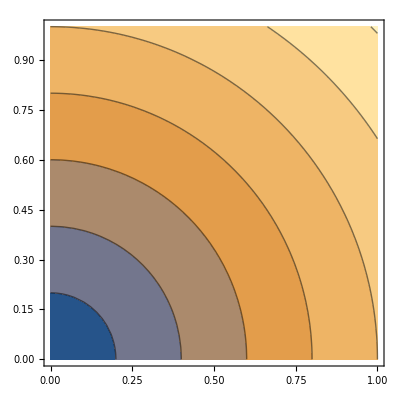

```mathematica
ContourPlot[Sqrt[(x)^2+(y)^2]/.t->0.001,{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,y_,t_]:= y
```

```mathematica
p[0,y,t]
```

y

```mathematica
p[1,y,t]
```

y

```mathematica
p[x,0,t]
```

0

```mathematica
p[x,1,t]
```

1

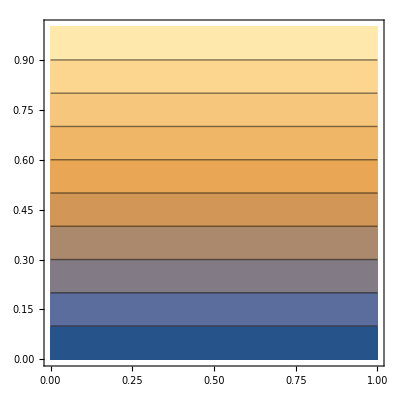

```mathematica
ContourPlot[p[x,y,t],{x,0,1},{y,0,1}]
```

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(y), x],D[(y), y]}//Simplify
```

{0,1}

```mathematica
Gradu[x_,y_,t_]:={{1,0},{0,1}}
```

Let us define ϵ (u) :

```mathematica
w=1/2*(Gradu[x,y,t]+Transpose[Gradu[x,y,t]])//Simplify
```

{{1,0},{0,1}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
σe=2mu w+lambda Tr[w]IdentityMatrix[2]//Simplify
```

{{2 (lambda+mu),0},{0,2 (lambda+mu)}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae[x_,y_,t_]:={{2 (lambda+mu),0},{0,2 (lambda+mu)}}
```

### Stress:

```mathematica
Sigmae[x,y,t]-alpha {{p[x,y,t],0},{0,p[x,y,t]}}//Simplify
```

{{2 (lambda+mu)-alpha y,0},{0,2 (lambda+mu)-alpha y}}

```mathematica
Sigma[x_,y_,t_]:={{2 (lambda+mu)-alpha y,0},{0,2 (lambda+mu)-alpha y}}
```

ContourPlot of the Magnitude of the first row of σ :

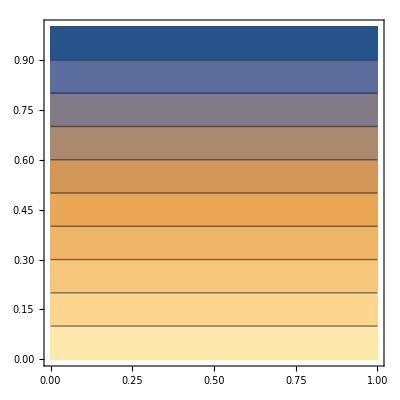

```mathematica
ContourPlot[2 (lambda+mu)-alpha y/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[2 (lambda+mu)-alpha y/.{lambda->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu[x,y,t]-Transpose[Gradu[x,y,t]])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

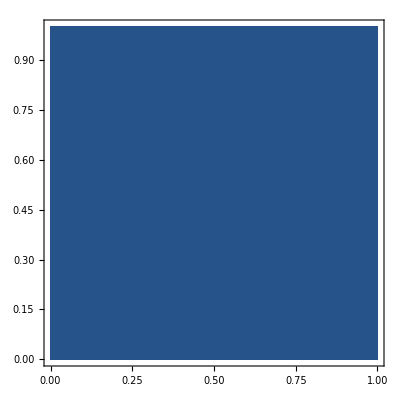

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
K = perm*IdentityMatrix[2];
```

```mathematica
-K.{D[p[x,y,t],x],D[p[x,y,t],y]}//Simplify
```

{0,-perm}

```mathematica
z[x_,y_,t_]:={0,-perm}
```

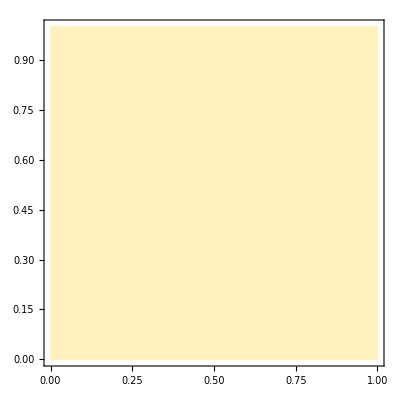

```mathematica
ContourPlot[perm/.perm->1,{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,y,t]
```

{{2 (lambda+mu)-alpha y,0},{0,2 (lambda+mu)-alpha y}}

```mathematica
-(D[2 (lambda+mu)-alpha y,x]+D[0,y])//Simplify
```

0

```mathematica
f1[x_,y_,t_]:=0
```

```mathematica
-(D[0,x]+D[2 (lambda+mu)-alpha y,y])//Simplify
```

alpha

```mathematica
f2[x_,y_,t_]:=alpha
```

### Source term q :

```mathematica
u[x,y,t]
```

{x,y}

```mathematica
z[x,y,t]
```

{0,-perm}

```mathematica
D[c0 p[x,y,t]+alpha (D[x,x]+D[y,y]),t]+D[0,x]+D[-perm,y]//Simplify
```

0